# A Stand Alone Module for Polynomial Gram-Schmidt

All we need to do is paste in the code from our other notebook!

```mathematica
PolyGS[w_,a_,b_,n_]:=Module[{B1,phi,Bk,Ck,GSStep},
B1[y_]:=Integrate[x*w[x],{x,a,b}]/Integrate[w[x],{x,a,b}];
phi={1&,(#-B1[#])&};
Bk[phi_]:=Integrate[x*w[x]*(phi[x])^2,{x,a,b}]/Integrate[w[x]*(phi[x]^2),{x,a,b}];
Ck[phi1_,phi2_]:=Integrate[x*w[x]*(phi2[x]*phi1[x]),{x,a,b}]/Integrate[w[x]*(phi1[x]^2),{x,a,b}];
NextGS[phi1_,phi2_]:=(#-Bk[phi2])*phi2[#]-Ck[phi1,phi2]*phi1[#]&;
GSStep:=AppendTo[phi,NextGS[phi[[Length[phi]-1]],phi[[Length[phi]]]]];
Do[GSStep,{i,n-2}];
phi
];
```

Let’s make sure it works by computing the first 4 Legendre polynomials.

```mathematica
Legendre=PolyGS[1&,1,3,4];
```

```mathematica
Legendres=Table[Legendre[[i]][x],{i,1,4}]
```

{1,-2+x,-1/3+(-2+x)^2,-4/15 (-2+x)+(-1/3+(-2+x)^2) (-2+x)}

```mathematica
Legendres[[3]]
```

-1/3+(-2+x)^2

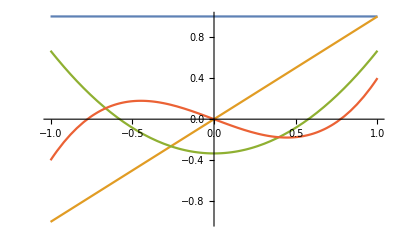

```mathematica
Plot[Legendres,{x,-1,1}]
```

Now we can bring up our code for computing the coefficients of the least squares approximation. Note that we have modified the inner product to take a weight function.

```mathematica
IP[f_,g_,w_,a_,b_]:=Integrate[w*f*g,{x,a,b}];
Proj[f_,g_,w_,a_,b_]:=IP[f,g,w,a,b]/IP[g,g,w,a,b];
LSCoefs[f_,polys_,w_,a_,b_]:=Table[Proj[f,polys[[i]],w,a,b],{i,1,Length[polys]}];
```

```mathematica
f[x_]:=Cos[x]
```

```mathematica
coefs=N[LSCoefs[f[x],Legendres,1,-1,1]]
```

{0.841471,0.,-0.465263,0.}

```mathematica
P=Sum[coefs[[i]]*Legendres[[i]],{i,1,Length[coefs]}]
```

0.841471-0.465263 (-1/3+x^2)

```mathematica
N[Expand[P]]
```

0.996559-0.465263 x^2

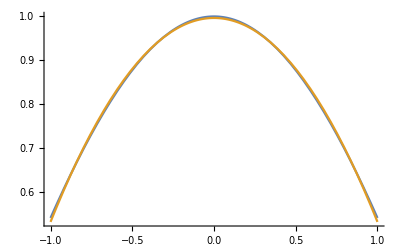

```mathematica
Plot[{f[x],P},{x,-1,1}]
```

Now we can have some fun! Remember the Chebyshev polynomials? We are now in a position to give a much better description of what they are and why they are important in Lagrange interpolation. But first, lets’s use our Gram-Schmidt module to compute the first four Chebyshev polynomials and then use them to find the least squares approximation for Cos[x].

```mathematica
Chebyshev=PolyGS[(1-#^2)^(-1/2)&,-1,1,5];
```

```mathematica
Chebyshevs=Table[Chebyshev[[i]][x],{i,1,5}];
Simplify[Chebyshevs]
```

{1,x,-1/2+x^2,-(3 x)/4+x^3,1/8-x^2+x^4}

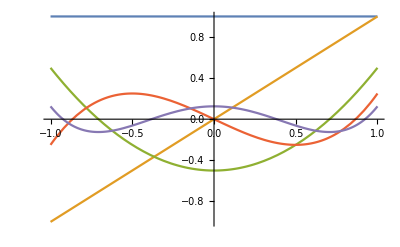

```mathematica
Plot[Chebyshevs,{x,-1,1}]
```

```mathematica
Table[IP[Chebyshevs[[i]],Chebyshevs[[j]],(1-x^2)^(-1/2),-1,1],{i,1,Length[Chebyshevs]},{j,1,Length[Chebyshevs]}]//MatrixForm
```

(π | 0 | 0 | 0 | 0
0 | π/2 | 0 | 0 | 0
0 | 0 | π/8 | 0 | 0
0 | 0 | 0 | π/32 | 0
0 | 0 | 0 | 0 | π/128)

{0.765198,0.,-0.459614,0.,0.0396262}

0.995005-0.459614 x^2

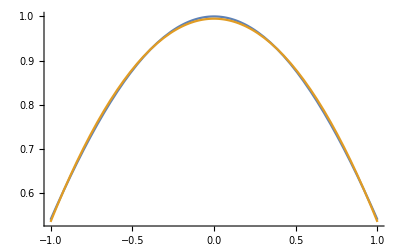

```mathematica
ChebyCoefs=N[LSCoefs[f[x],Chebyshevs,(1-x^2)^(-1/2),-1,1]]
CP=Sum[ChebyCoefs[[i]]*Chebyshevs[[i]],{i,1,Length[coefs]}];
N[Expand[CP]]
Plot[{f[x],CP},{x,-1,1}]
```

We get the same polynomial! As well we should, because all we have done is change basis in the subspace of polynomials of degree at most 3.

Now, let’s look at the roots of the Chebyshev polynomials.

```mathematica
NSolve[Chebyshevs[[5]]==0,x]
```

{{x→-0.92388},{x→-0.382683},{x→0.382683},{x→0.92388}}

Recall that back when we did Lagrange interpolation we had a formula for the “Chebyshev nodes.”

```mathematica
a=-1;
b=1;
n=3;
ChebyNodes := Table[(1/2)*(a + b) + (1/2)(b-a)Cos[(2i+1)Pi/(2n+2)],{i,0,n}]
```

```mathematica
N[ChebyNodes]
```

{0.92388,0.382683,-0.382683,-0.92388}

They are the same! The nth degree Lagrange error is minimized (in general) when we choose the nodes to be the roots of the nth degree Chebyshev polynomial.

The Chebyshev polynomials have some nice properties. One of which is that they have predictable extrema.

```mathematica
Table[Maximize[{Chebyshevs[[i]],x^2≤1},x][[1]],{i,1,5}]
```

{1,1,1/2,1/4,1/8}

```mathematica
Table[Minimize[{Chebyshevs[[5]],x^2≤1},x][[1]],{i,1,5}]
```

{-1/8,-1/8,-1/8,-1/8,-1/8}